```mathematica
DSolve[{y1'[t]==32*y1[t]+66y2[t]+(2*t)/3+2/3,y2'[t]==-66y1[t]-133y2[t]-t/3-1/3,y1[0]==1/3,y2[0]==1/3},{y1,y2},{t,0,0.5}]
```

{{y1→Function[{t},1/3 (-ⅇ^(-100 t)+2 ⅇ^-t+2 t)],y2→Function[{t},1/3 (2 ⅇ^(-100 t)-ⅇ^-t-t)]}}

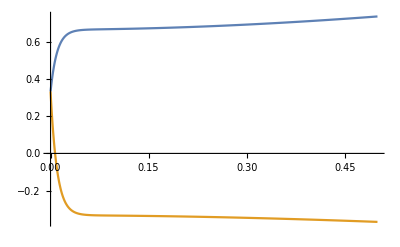

```mathematica
Plot[Evaluate[{y1[x],y2[x]}/.%],{x,0,.5}]
```